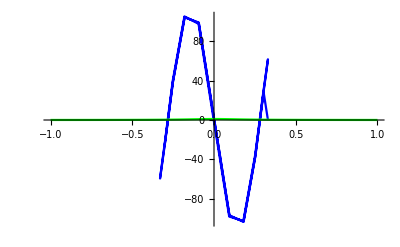

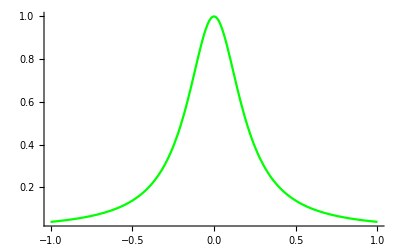

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
list = ReadList["grid.txt", Number, RecordLists->True];
uni = Partition[Riffle[list[[1]], list[[2]]], 2];
plot1= ListLinePlot[uni, PlotStyle->Red];
cheb = Partition[Riffle[list[[3]], list[[4]]], 2];
plot2 =ListLinePlot[cheb, PlotStyle->Blue];
plot3 = Plot[1 / (1+25*x*x),{x,-1,1}, PlotStyle->Green];
Show[plot2,plot3, PlotRange->All]
Show[plot1,plot3, PlotRange->All]
```